```mathematica
dir ="/Users/laik/Documents/fall2022/Images/locule_scans/cropped/";
filename ="lalo10000";
img =Import[dir <> filename <> ".JPG"];
crans=img;
```

```mathematica
sizeCircle=-Graphics-;(*1 inch diameter*)
binSizeCircle = ColorNegate[Binarize[sizeCircle]];
Total[binSizeCircle]
diameterOfSizeCircle = Max[Total /@ ImageData[binSizeCircle]]
(diameterOfSizeCircle/2.0)^2*Pi
```

273830.

588

271547.

```mathematica
(*Increase the contrast to better see the hollow areas*)
ContrastCrans = ImageAdjust[crans,5];
(*Use the kuwahara filter to smooth the colors while preserving edges*)
KuwaCrans = KuwaharaFilter[ContrastCrans, 5]
```

-Graphics-

```mathematica
(*Binarize at different treshold values, add the results together because some holes show up better at different levels.
Use the Watershed segmentation method to get the segments of the image that are the hollow locules.
Do each color channel individually because each color channel also has different holes. 
The masks are all added together to create one final mask of the inner hollow area.
This method was invented purely through experimentation of different values and noticing what worked best*)
BinCrans = Binarize[ColorSeparate[ContrastCrans][[1]],#]&/@Range[0,1, 0.05];
mask1 = Total[ColorNegate[Binarize[Colorize[WatershedComponents[#,Method->{"MinimumSaliency",0.3}]]]]&/@BinCrans];
mask1 = DeleteSmallComponents[mask1,200];
```

```mathematica
BinCrans = Binarize[ColorSeparate[ContrastCrans][[2]],#]&/@Range[0,1, 0.05];
mask2 = Total[ColorNegate[Binarize[Colorize[WatershedComponents[#,Method->{"MinimumSaliency",0.3}]]]]&/@BinCrans];
mask2 = DeleteSmallComponents[mask2, 200];
```

```mathematica
BinCrans = Binarize[ColorSeparate[ContrastCrans][[3]],#]&/@Range[0,1, 0.05];
mask3 = Total[ColorNegate[Binarize[Colorize[WatershedComponents[#,Method->{"MinimumSaliency",0.3}]]]]&/@BinCrans];
mask3 = DeleteSmallComponents[mask3, 200];
```

```mathematica
mask = mask1+mask2+mask3
```

-Graphics-

```mathematica
(*Create mask of stamp/footprint of the full cranberry slice*)
fullCranContours = ContourDetect[crans, 0.2];
finalCranMask = DeleteSmallComponents[ColorNegate[fullCranContours + mask],100]
```

-Graphics-

```mathematica
(*Partition the image into each individual cranberry to calculate data about each cranberry*)
origCransPartition = Flatten[ImagePartition[crans,{ImageDimensions[crans][[1]]/5, ImageDimensions[crans][[2]]/5}]];
```

```mathematica
cranPartition =Flatten[ImagePartition[finalCranMask,{ImageDimensions[finalCranMask][[1]]/5, ImageDimensions[finalCranMask][[2]]/5}]];
```

```mathematica
fullCranPartition = Flatten[ImagePartition[DeleteSmallComponents[ColorNegate[fullCranContours], 100],{ImageDimensions[fullCranContours][[1]]/5, ImageDimensions[fullCranContours][[2]]/5}]];
```

```mathematica
hollowCranSizes = Total /@ Flatten /@ImageData /@ cranPartition;
fullCranSizes =  Total /@ Flatten /@ImageData /@ fullCranPartition;
```

```mathematica
(*Average color*)
averageCranColor = Range[Length[origCransPartition]];
Do[
averageCranColor[[i]] = ImageMeasurements[origCransPartition[[i]], "Mean",  Masking -> fullCranPartition[[i]]];
,{i,1,Length[averageCranColor]}]
averageCranColor;
shownAvgCranColor =Graphics[{RGBColor[#],Disk[]}] &/@ averageCranColor;
```

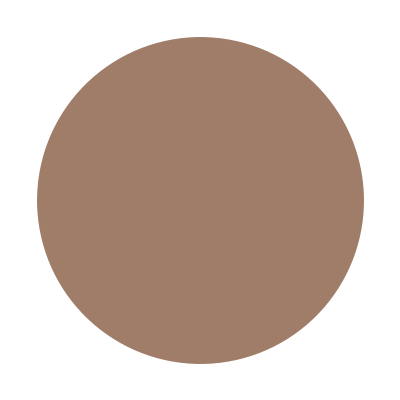
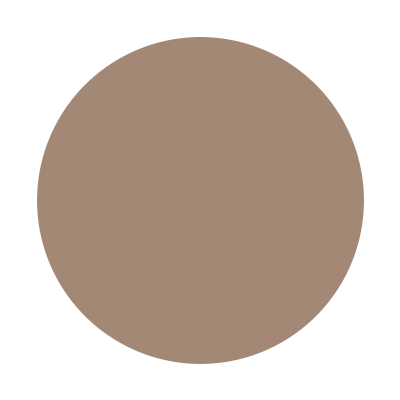
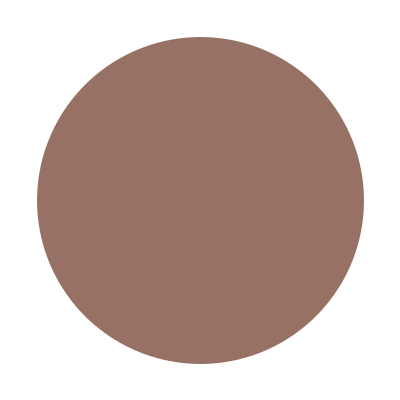
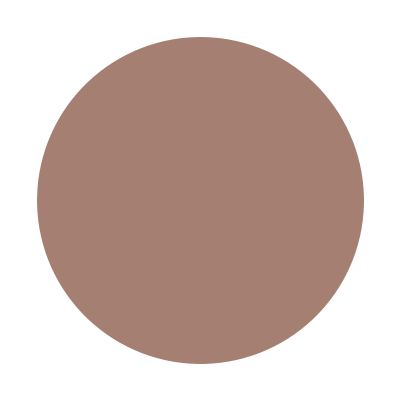
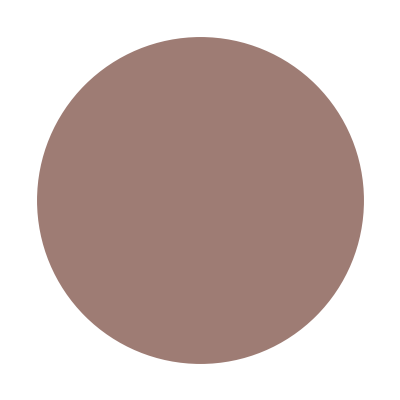
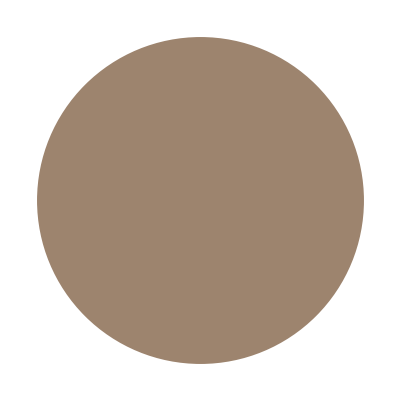
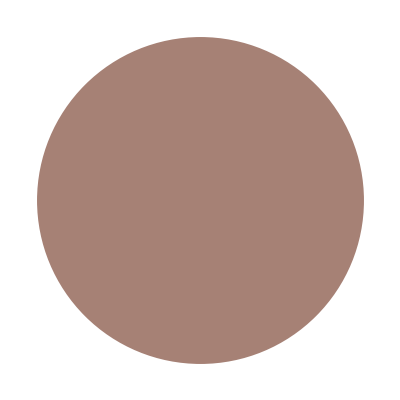
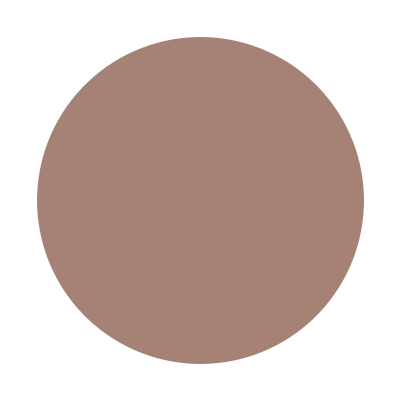
(-Graphics- | -Graphics- | {0.629045,0.490237,0.409673} | -Graphics- | 89656 | 25727. | 63929.
-Graphics- | -Graphics- | {0.637655,0.537837,0.457426} | -Graphics- | 93904 | 34694. | 59210.
-Graphics- | -Graphics- | {0.594641,0.442755,0.396793} | -Graphics- | 65762 | 15199. | 50563.
-Graphics- | -Graphics- | {0.648107,0.50037,0.448677} | -Graphics- | 80016 | 30211. | 49805.
-Graphics- | -Graphics- | {0.61964,0.486623,0.454681} | -Graphics- | 96844 | 26743. | 70101.
-Graphics- | -Graphics- | {0.617054,0.517255,0.43233} | -Graphics- | 101512 | 42254. | 59258.
-Graphics- | -Graphics- | {0.651714,0.505684,0.460512} | -Graphics- | 87861 | 25760. | 62101.
-Graphics- | -Graphics- | {0.646488,0.510568,0.458161} | -Graphics- | 99377 | 29787. | 69590.
-Graphics- | -Graphics- | {0.644695,0.526096,0.432367} | -Graphics- | 84184 | 33565. | 50619.
-Graphics- | -Graphics- | {0.655102,0.532552,0.496618} | -Graphics- | 77087 | 15667. | 61420.
-Graphics- | -Graphics- | {0.657123,0.536608,0.434431} | -Graphics- | 77276 | 31134. | 46142.
-Graphics- | -Graphics- | {0.620344,0.490773,0.463878} | -Graphics- | 82538 | 21970. | 60568.
-Graphics- | -Graphics- | {0.633743,0.502053,0.465163} | -Graphics- | 73841 | 20379. | 53462.
-Graphics- | -Graphics- | {0.601676,0.467033,0.419625} | -Graphics- | 63550 | 22563. | 40987.
-Graphics- | -Graphics- | {0.642768,0.495675,0.445847} | -Graphics- | 63440 | 16495. | 46945.
-Graphics- | -Graphics- | {0.644635,0.494458,0.437518} | -Graphics- | 50759 | 12372. | 38387.
-Graphics- | -Graphics- | {0.641255,0.532634,0.444422} | -Graphics- | 98239 | 25790. | 72449.
-Graphics- | -Graphics- | {0.635496,0.505641,0.445315} | -Graphics- | 92029 | 32921. | 59108.
-Graphics- | -Graphics- | {0.636196,0.503846,0.447399} | -Graphics- | 83290 | 29115. | 54175.
-Graphics- | -Graphics- | {0.649058,0.521579,0.456114} | -Graphics- | 93019 | 23534. | 69485.
-Graphics- | -Graphics- | {0.658339,0.53928,0.480897} | -Graphics- | 79402 | 21610. | 57792.
-Graphics- | -Graphics- | {0.664,0.550071,0.493468} | -Graphics- | 74496 | 15234. | 59262.
-Graphics- | -Graphics- | {0.591627,0.472875,0.409227} | -Graphics- | 88610 | 34548. | 54062.
-Graphics- | -Graphics- | {0.661835,0.543895,0.468333} | -Graphics- | 86209 | 16125. | 70084.
-Graphics- | -Graphics- | {0.613372,0.446738,0.417995} | -Graphics- | 82003 | 21312. | 60691.)

```mathematica
(*Data recorded via some analysis*)
data =Transpose[{origCransPartition, shownAvgCranColor,averageCranColor,cranPartition, fullCranSizes, fullCranSizes - hollowCranSizes, hollowCranSizes}];
data // MatrixForm
(*
Original image, mask, total area, hollow area, non-hollow area
*)
```

```mathematica
Export["Documents/fall2022/Output/"<>filename<>".csv",
Join[{{"Full area", "Non-hollow area", "Hollow area", "Avg. Color"}},Transpose[{fullCranSizes, fullCranSizes - hollowCranSizes, hollowCranSizes, averageCranColor}]], 
"csv"]
```

Documents/fall2022/Output/lalo10000.csv

```mathematica
img=Rasterize[MatrixForm[data]];
Export["Documents/fall2022/Output/"<>filename<>"_out.jpg",img]
```

Documents/fall2022/Output/lalo10000_out.jpg